## Functions

## Helpers

```mathematica
(*Helper to import files in a more useful format*)
ImportData[file_]:=Module[{newdat},
newdat=Import[file];
ToExpression[newdat]
]
```

```mathematica
(*Set up the monod resource usage function*)
Monod[resource_,maxr_,conversion_,halfsat_]:=Module[{},(maxr/conversion)*resource/(resource+halfsat)];
```

```mathematica
(*Determines which cells are neighbors of a given patch*)
NBMaker[location_,hood_,size_]:=Module[{nblist},
nblist={};
Do[
If[0<location[[1,1]]+i<size+1,AppendTo[nblist,{location[[1,1]]+i,location[[1,2]]}]];
If[0<location[[1,2]]+i<size+1,AppendTo[nblist,{location[[1,1]],location[[1,2]]+i}]],
{i,-hood,hood}];
Return[Delete[nblist,Position[nblist,location[[1]]]]]];
```

```mathematica
(*returns all the neighbor relationships*)
Neighbors[patch_,mat_,hood_,size_]:=Module[{location,nbs},
location=Position[mat,patch];

nbs=NBMaker[location,hood,size];

Return[Table[mat[[nbs[[i,1]],nbs[[i,2]]]],{i,Length[nbs]}]]]
```

```mathematica
(*This function relates resource 1 to resource 2 along the line explained in figure 2*)
CrossSection[supply1_]:=10-supply1
```

```mathematica
(*This function returns the proportio of species 1 in the final patch*)
Prop[finals_]:=finals[[1]]/Total[finals]
```

## Within a patch

```mathematica
(*This function gives the dynamics for a single patch between disturbance events*)
OnePatch[time_,inits_]:=Module[{s1,s2,eq,eqN,eqns,ics,unks,sol},
(*identify the supply point*)
{s1,s2}=inits[[3;;4]];
(*figure out the equilibrium value*)
eq={Max[rstar11,rstar21],Max[rstar12,rstar22]};
(*Set up the equations, initial conditions, and unknowns*)
eqns={R1'[t]==a1*(s1+nc11*N1[t]+nc21*N2[t]-R1[t])-Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]*N1[t]*y11-Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]*N2[t]*y21,
R2'[t]==a2*(s2+nc22*N2[t]+nc12*N1[t]-R2[t])-Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]*N1[t]*y12-Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]*N2[t]*y22,
N1'[t]==N1[t]*Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]-m1*N1[t],
N2'[t]==N2[t]*Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]-m2*N2[t]};
ics={R1[0]==inits[[3]],R2[0]==inits[[4]],N1[0]==inits[[1]],N2[0]==inits[[2]]};
unks={R1[t],R2[t],N1[t],N2[t]};
(*Solve the differential equations*)
sol=NDSolve[Join[eqns,ics],unks,{t,0,time}];
(*Return the results*)
Return[sol]]
```

```mathematica
(*For figure 3*)
```

```mathematica
SlimPatch[time_,inits_,s1_,s2_]:=Module[{eqns,ics,unks,sol},

eqns={R1'[t]==a1*(s1+nc11*N1[t]+nc21*N2[t]-R1[t])-Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]*N1[t]*y11-Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]*N2[t]*y21,
R2'[t]==a2*(s2+nc22*N2[t]+nc12*N1[t]-R2[t])-Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]*N1[t]*y12-Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]*N2[t]*y22,
N1'[t]==N1[t]*Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]-m1*N1[t],
N2'[t]==N2[t]*Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]-m2*N2[t]};
ics={R1[0]==inits[[3]],R2[0]==inits[[4]],N1[0]==inits[[1]],N2[0]==inits[[2]]};
unks={R1[t],R2[t],N1[t],N2[t]};
sol=NDSolve[Join[eqns,ics],unks,{t,0,time}];
Return[Evaluate[{N1[t],N2[t],R1[t],R2[t]}/.sol/.{t->time}]]]
```

```mathematica
(*Shorter version of one patch for the cross section plots in figures 4 and 5*)
SlimPatchCross[time_,inits_,s1_,s2_ ,nclist_]:=Module[{eqns,ics,unks,sol},
eqns={R1'[t]==a1*(s1+nclist[[1]]*N1[t]+nclist[[3]]*N2[t]-R1[t])-Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]*N1[t]*y11-Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]*N2[t]*y21,
R2'[t]==a2*(s2+nclist[[4]]*N2[t]+nclist[[2]]*N1[t]-R2[t])-Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]*N1[t]*y12-Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]*N2[t]*y22,
N1'[t]==N1[t]*Min[Monod[R1[t],r11,y11,k11],Monod[R2[t],r12,y12,k12]]-m1*N1[t],
N2'[t]==N2[t]*Min[Monod[R1[t],r21,y21,k21],Monod[R2[t],r22,y22,k22]]-m2*N2[t]};
ics={R1[0]==inits[[3]],R2[0]==inits[[4]],N1[0]==inits[[1]],N2[0]==inits[[2]]};
unks={R1[t],R2[t],N1[t],N2[t]};
sol=NDSolve[Join[eqns,ics],unks,{t,0,time}];
Return[Evaluate[{N1[t],N2[t],R1[t],R2[t]}/.sol/.{t->time}]]]
```

## Metacommunity wrapper functions

```mathematica
(*for figure 3*)
```

```mathematica
MCSim[patches_,sval1_,sval2_,isol_]:=Module[{size,names,m,disturbmat,start,plist,sols,species,reses,species2},
size=patches;
names=Table[i,{i,size*size}];
m=Partition[names,size];

disturbmat=Table[{n,names[[j]],RandomChoice[{1-dist,dist}->{0,1}]},{n,1,niter},{j,1,Length[names]}];
(*Print[disturbmat];*)
Table[start[i]={RandomReal[{.001,.1}],RandomReal[{.001,.1}],sval1,sval2},{i,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)

If[isol==False,Do[
Table[sols[names[[i]]]=SlimPatch[tstep,start[i],sval1,sval2],{i,size^2}];

Table[species[i]=sols[i][[1,1;;2]],{i,size^2}];
Table[reses[i]=sols[i][[1,3;;4]],{i,size^2}];
Table[species2[i]=species[i],{i,size^2}];

Table[If[disturbmat[[iter,j,3]]==1,species2[j]=Mean[Table[species[i],{i,Neighbors[j,m,1,size]}]]/100],{j,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)
Table[start[i]=Join[species2[i],reses[i]],{i,size^2}],{iter,niter}],
Do[
Table[sols[names[[i]]]=SlimPatch[tstep,start[i],sval1,sval2],{i,size^2}];

Table[species[i]=sols[i][[1,1;;2]],{i,size^2}];
Table[reses[i]=sols[i][[1,3;;4]],{i,size^2}];
Table[species2[i]=species[i],{i,size^2}];

Table[If[disturbmat[[iter,j,3]]==1,species2[j]=species[j]/100],{j,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)
Table[start[i]=Join[species2[i],reses[i]],{i,size^2}],{iter,niter}]];

Return[Table[Prop[species2[i]],{i,size^2}]]
]
```

```mathematica
(*This is the metacommunity wrapper function for figure 4*)
MCSimCross[patches_,sup1_,nclist_,isol_]:=Module[{size,names,m,sval1,sval2,disturbmat,start,plist,sols,species,reses,species2},
size=patches;
(*name all the patches*)
names=Table[i,{i,size*size}];
(*Make the matrix*)
m=Partition[names,size];
(*Figure out the supply points*)
sval1=sup1;
sval2=CrossSection[sup1];
(*pre-draw the random disturbance*)
disturbmat=Table[{n,names[[j]],RandomChoice[{1-dist,dist}->{0,1}]},{n,1,niter},{j,1,Length[names]}];
(*Create the starting conditions for each patch*)
Table[start[i]={RandomReal[{.001,.1}],RandomReal[{.001,.1}],sval1,sval2},{i,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)
(*Switch for dispersal or isolation*)
If[isol==False,(*instructions for iterations with dispersal*)Do[
(*dynamics within each patch*)
Table[sols[names[[i]]]=SlimPatchCross[tstep,start[i],sval1,sval2,nclist],{i,size^2}];
(*separate the species results from the resource results*)
Table[species[i]=sols[i][[1,1;;2]],{i,size^2}];
Table[reses[i]=sols[i][[1,3;;4]],{i,size^2}];
Table[species2[i]=species[i],{i,size^2}];
(*if patches are disturbed, reset their residents*)
Table[If[disturbmat[[iter,j,3]]==1,species2[j]=Mean[Table[species[i],{i,Neighbors[j,m,1,size]}]]/100],{j,size^2}];
(*remake the starting conditions with the disturbance and do it all over again*)
Table[start[i]=Join[species2[i],reses[i]],{i,size^2}],{iter,niter}],
Do[ (*This is the same thing only after a disturbance things just get knocked down to 1% of their previous density*)
Table[sols[names[[i]]]=SlimPatchCross[tstep,start[i],sval1,sval2,nclist],{i,size^2}];

Table[species[i]=sols[i][[1,1;;2]],{i,size^2}];
Table[reses[i]=sols[i][[1,3;;4]],{i,size^2}];
Table[species2[i]=species[i],{i,size^2}];

Table[If[disturbmat[[iter,j,3]]==1,species2[j]=species[j]/100],{j,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)
Table[start[i]=Join[species2[i],reses[i]],{i,size^2}],{iter,niter}]];
(*Return the poroportion of each species in each patch at the end of it all*)
Return[Table[Prop[species2[i]],{i,size^2}]]
]
```

```mathematica
(*variable dispersal for figure 5*)
```

```mathematica
MCSimCrossD[patches_,sup1_,nclist_,disp_]:=Module[{size,names,m,sval1,sval2,disturbmat,start,plist,sols,species,reses,species2},
size=patches;
names=Table[i,{i,size*size}];
m=Partition[names,size];
sval1=sup1;
sval2=CrossSection[sup1];
disturbmat=Table[{n,names[[j]],RandomChoice[{1-dist,dist}->{0,1}]},{n,1,niter},{j,1,Length[names]}];
(*Print[disturbmat];*)
Table[start[i]={RandomReal[{.001,.1}],RandomReal[{.001,.1}],sval1,sval2},{i,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)

Do[
Table[sols[names[[i]]]=SlimPatchCross[tstep,start[i],sval1,sval2,nclist],{i,size^2}];
Table[species[i]=sols[i][[1,1;;2]],{i,size^2}];
Table[reses[i]=sols[i][[1,3;;4]],{i,size^2}];
Table[species2[i]=species[i],{i,size^2}];
Table[If[disturbmat[[iter,j,3]]==1,species2[j]=(1-disp)species[j]/100+disp*Mean[Table[species[i],{i,Neighbors[j,m,1,size]}]]/100],{j,size^2}];
(*Print[Table[start[i],{i,size^2}]];*)
Table[start[i]=Join[species2[i],reses[i]],{i,size^2}],{iter,niter}];


Return[Table[Prop[species2[i]],{i,size^2}]]
]
```

```mathematica
(*This function asks if there is coexistence within a patch*)
Coexist[val_]:=Module[{cox},
cox=Table[If[.99>val[[i]]>.01,1,0],{i,Length[val]}];
Return[cox]]
```

## Output

```mathematica
Outputter[patches_,sval1_,sval2_,isol_]:=Module[{list},
Print[{sval1,sval2}];
list=MCSim[patches,sval1,sval2,isol];
Return[{Mean[list],Variance[list]/Mean[list],Mean[Coexist[list]]}]]
```

```mathematica
(*This function wraps it all up and returns within patch, winner,  coexistence, and variance in coexistence between patches*)
OutputterCross[patches_,sval1_,nlist_,isol_]:=Module[{list},
Print[{sval1,nlist}];
list=MCSimCross[patches,sval1,nlist,isol];
Return[{Mean[list],Variance[list]/Mean[list],Mean[Coexist[list]]}]]
```

```mathematica
OutputterCrossD[patches_,sup1_,nclist_,disp_]:=Module[{list},
Print[{sup1,nclist}];
list=MCSimCrossD[patches,sup1,nclist,disp];
Return[{Mean[list],Variance[list]/Mean[list],Mean[Coexist[list]]}]]
```

## Parameters-Choose One!

## Priority Effects

```mathematica
Monod[resource_,maxr_,conversion_,halfsat_]:=Module[{},(maxr/conversion)*resource/(resource+halfsat)];
tmax=1000;
a1=1;(*the inflow rate of R1*)
a2=1;(*the inflow rate of R2*)
r11=3; (*the maximum growth rate of N1 on R1*)
r12=1.1; (*the maximum growth rate of N2 on R2*)
r21=1.1; (*the maximum growth rate of N1 on R1*)
r22=3; (*the maximum growth rate of N2 on R2*)
y11=2;(*the conversion of species 1 to resource 1*)
y12=1.3;(*the conversion of species 1 to resource 2*)
y21=1;(*the conversion of species 2 to resource 1*)
y22=1.4;(*the conversion of species 2 to resource 2*)
k11=1;(*the half saturation constant of N1 on R1*)
k12=1;(*the half saturation constant of N1 on R2*)
k21=1;(*the half saturation constant of N2 on R1*)
k22=1;
m1=.3;(*the mortality rate of N1*)
m2=.3;(*the mortality rate of N2*)
rstar11=m1*k11/(r11/y11-m1)(*species 1 on resource 1*)
rstar12=m1*k12/(r12/y12-m1)(*species 1 on resource 2*)
rstar21=m2*k21/(r21/y21-m2)(*species 2 on resource 1*)
rstar22=m2*k22/(r22/y22-m2)(*species 2 on resource 2*)
eq={Max[rstar11,rstar21],Max[rstar12,rstar22]};
nc11=0;(*niche construction effect of species 1 on resource 1*)
nc12=0;(*niche construction effect of species 1 on resource 2*)
nc21=0;(*niche construction effect of species 2 on resource 1*)
nc22=0;(*niche construction effect of species 2 on resource 2*)
```

0.25

0.549296

0.375

0.162791

```mathematica
{eqN}=Solve[{0==a1*(s1+nc11*N1+nc21*N2-eq[[1]])-m1*N1*y11-m2*N2*y21,0==a2*(s2+nc22*N2+nc12*N1-eq[[2]])-m1*N1*y12-m2*N2*y22},{N1,N2}]
C11=Min[Monod[eq[[1]],r11,y11,k11],Monod[eq[[2]],r12,y12,k12]]*y11;(*species 1 per-capita consumption rate of resource 1 at equilibrium*)
C12=Min[Monod[eq[[1]],r11,y11,k11],Monod[eq[[2]],r12,y12,k12]]*y12;(*species 1 per-capita consumption rate of resource 2 at equilibrium*)
C21=Min[Monod[eq[[1]],r21,y21,k21],Monod[eq[[2]],r22,y22,k22]]*y21;(*species 2 per-capita consumption rate of resource 1 at equilibrium*)
C22=Min[Monod[eq[[1]],r21,y21,k21],Monod[eq[[2]],r22,y22,k22]]*y22; (*species 2 per-capita consumption rate of resource 2 at equilibrium*)
```

{{N1→0.0539906+3.11111 s1-2.22222 s2,N2→-1.35798-2.88889 s1+4.44444 s2}}

```mathematica
dist=0.02 (*disturbance rate*)
niter=200; (*number of iterations*)
i1=.1; (*average initial abundance of species 1*)
i2=.1;(*average initial abundance of species 2*)
tstep=10(*Time between potential disturbance events*)
```

0.02

10

## Coexistence

```mathematica
tmax=1000;
a1=1;(*the inflow rate of R1*)
a2=1;(*the inflow rate of R2*)
r11=3; (*the maximum growth rate of N1 on R1*)
r12=1.1; (*the maximum growth rate of N2 on R2*)
r21=1.1; (*the maximum growth rate of N1 on R1*)
r22=3; (*the maximum growth rate of N2 on R2*)
y11=1.3;(*the conversion of species 1 to resource 1*)
y12=2;(*the conversion of species 1 to resource 2*)
y21=1.4;(*the conversion of species 2 to resource 1*)
y22=1;(*the conversion of species 2 to resource 2*)
k11=1;(*the half saturation constant of N1 on R1*)
k12=1;(*the half saturation constant of N1 on R2*)
k21=1;(*the half saturation constant of N2 on R1*)
k22=1
m1=.3;(*the mortality rate of N1*)
m2=.3;(*the mortality rate of N2*)
rstar11=m1*k11/(r11/y11-m1)(*species 1 on resource 1*)
rstar12=m1*k12/(r12/y12-m1)(*species 1 on resource 2*)
rstar21=m2*k21/(r21/y21-m2)(*species 2 on resource 1*)
rstar22=m2*k22/(r22/y22-m2)(*species 2 on resource 2*)
eq={Max[rstar11,rstar21],Max[rstar12,rstar22]};
nc11=0;(*niche construction effect of species 1 on resource 1*)
nc12=0;(*niche construction effect of species 1 on resource 2*)
nc21=0;(*niche construction effect of species 2 on resource 1*)
nc22=0;(*niche construction effect of species 2 on resource 2*)
```

```mathematica
start1=6;
start2=4;
```

```mathematica
s1=start1;
s2=start2
```

4

```mathematica
s1
```

6

```mathematica
{eqN}=Solve[{0==(a1+nc11*N1+nc21*N2)*(s1-eq[[1]])-m1*N1*y11-m2*N2*y21,0==(a2+nc22*N2+nc12*N1)*(s2-eq[[2]])-m1*N1*y12-m2*N2*y22},{N1,N2}]
C11=Min[Monod[eq[[1]],r11,y11,k11],Monod[eq[[2]],r12,y12,k12]]*y11;(*species 1 per-capita consumption rate of resource 1 at equilibrium*)
C12=Min[Monod[eq[[1]],r11,y11,k11],Monod[eq[[2]],r12,y12,k12]]*y12;(*species 1 per-capita consumption rate of resource 2 at equilibrium*)
C21=Min[Monod[eq[[1]],r21,y21,k21],Monod[eq[[2]],r22,y22,k22]]*y21;(*species 2 per-capita consumption rate of resource 1 at equilibrium*)
C22=Min[Monod[eq[[1]],r21,y21,k21],Monod[eq[[2]],r22,y22,k22]]*y22; (*species 2 per-capita consumption rate of resource 2 at equilibrium*)
```

{{N1→-3.24967,N2→15.8327}}

```mathematica
dist=0.02
niter=200;
i1=.1;
i2=.1;
tstep=10;
```

0.02

## Make ZNGI Plots

## Choose the niche construction

```mathematica
strength=.23
```

0.23

### None

```mathematica
nc11=0;(*niche construction effect of species 1 on resource 1*)
nc12=0;(*niche construction effect of species 1 on resource 2*)
nc21=0;(*niche construction effect of species 2 on resource 1*)
nc22=0;(*niche construction effect of species 2 on resource 2*)
```

### Friendly

```mathematica
nc11=strength;(*niche construction effect of species 1 on resource 1*)
nc12=0;(*niche construction effect of species 1 on resource 2*)
nc21=0;(*niche construction effect of species 2 on resource 1*)
nc22=strength;(*niche construction effect of species 2 on resource 2*)
```

### Selfish

```mathematica
nc11=0;(*niche construction effect of species 1 on resource 1*)
nc12=strength;(*niche construction effect of species 1 on resource 2*)
nc21=strength;(*niche construction effect of species 2 on resource 1*)
nc22=0;(*niche construction effect of species 2 on resource 2*)
```

## Plots

```mathematica
{eqN}=Solve[{0==a1*(s1+nc11*N1+nc21*N2-eq[[1]])-m1*N1*y11-m2*N2*y21,0==a2*(s2+nc22*N2+nc12*N1-eq[[2]])-m1*N1*y12-m2*N2*y22},{N1,N2}]
C11=Min[Monod[eq[[1]],r11,y11,k11],Monod[eq[[2]],r12,y12,k12]]*y11;(*species 1 per-capita consumption rate of resource 1 at equilibrium*)
C12=Min[Monod[eq[[1]],r11,y11,k11],Monod[eq[[2]],r12,y12,k12]]*y12;(*species 1 per-capita consumption rate of resource 2 at equilibrium*)
C21=Min[Monod[eq[[1]],r21,y21,k21],Monod[eq[[2]],r22,y22,k22]]*y21;(*species 2 per-capita consumption rate of resource 1 at equilibrium*)
C22=Min[Monod[eq[[1]],r21,y21,k21],Monod[eq[[2]],r22,y22,k22]]*y22; (*species 2 per-capita consumption rate of resource 2 at equilibrium*)
```

{{N1→2.72066,N2→3.30869}}

```mathematica
start1=3;
start2=3;
```

```mathematica
s1=start1;
s2=start2;
```

3

```mathematica
tmax=1000;
tgraph=300;
```

1000

300

```mathematica
n
```

n

```mathematica
sol=OnePatch[tmax,{.1,.01,start1,start2}];
```

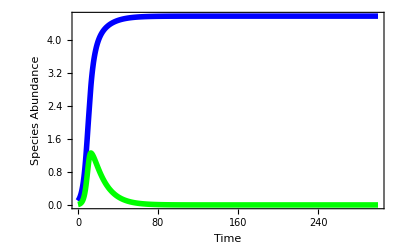

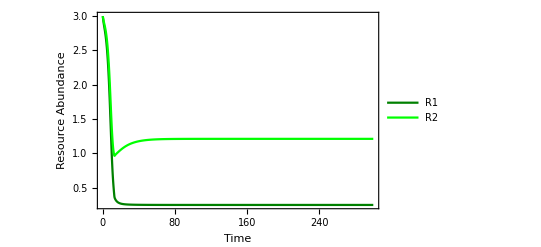

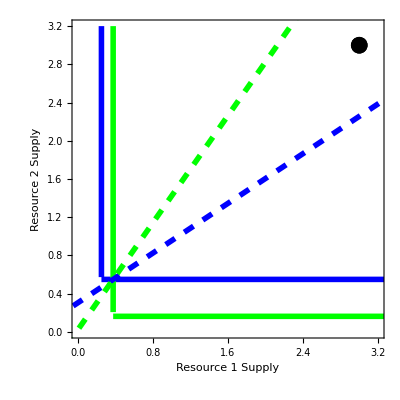

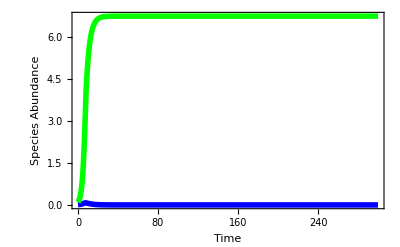

```mathematica
plotN1=Plot[Evaluate[{N1[t],N2[t]}/.sol],{t,0,tgraph},PlotRange->All,PlotStyle->{{RGBColor[0,0,1],Thickness[.01]},{RGBColor[0,1,0],Thickness[.01]}},Frame->{True,True,False,False},LabelStyle->Directive[FontFamily->"Geneva",FontSize->16,FontColor->Black],FrameLabel->{"Time","Species Abundance"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black]]

plotR=Plot[Evaluate[{R1[t],R2[t]}/.sol],{t,0,tgraph},PlotRange->All,PlotStyle->{Darker[Green,.5],Green},PlotLegends->LineLegend[{Darker[Green,.5],Green},{"R1","R2"}],Frame->{True,True,False,False},LabelStyle->Directive[FontFamily->"Geneva",FontSize->16,FontColor->Black],FrameLabel->{"Time","Resource Abundance"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black]]
zngiplot1=Plot[{10^5(r1-rstar11)+rstar12,rstar12},{r1,rstar11,12},PlotRange->{{0,3.2},{0,3.2}},PlotStyle->Directive[{RGBColor[0,0,1],Thickness[.01]}]];
zngiplot2=Plot[{10^5*(r1-rstar21)+rstar22,rstar22},{r1,rstar21,22},PlotRange->{{0,3.2},{0,3.2}},PlotStyle->Directive[{RGBColor[0,1,0],Thickness[.01]}]];
ssplot=ListPlot[{{start1,start2}},PlotStyle->Directive[Black,PointSize[0.03]],LabelStyle->Directive[FontFamily->"Geneva",FontSize->12,FontColor->Black]];
plotZ=Show[{zngiplot1,zngiplot2,ssplot,Graphics[{RGBColor[0,0,1],Dashing[.02],Thickness[.01],InfiniteLine[eq,{(C11-nc11)N1/.eqN,(C12-nc12)N1/.eqN}]}],Graphics[{RGBColor[0,1,0],Dashing[.02],Thickness[.01],InfiniteLine[eq,{(C21-nc21)N2/.eqN,(C22-nc22)N2/.eqN}]}]},Frame->{True,True,False,False},LabelStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameLabel->{"Resource 1 Supply","Resource 2 Supply"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],AspectRatio->1]
sol=OnePatch[tmax,{.01,.1,start1,start2}];
plotN2=Plot[Evaluate[{N1[t],N2[t]}/.sol],{t,0,tgraph},PlotRange->All,PlotStyle->{{RGBColor[0,0,1],Thickness[.01]},{RGBColor[0,1,0],Thickness[.01]}},Frame->{True,True,False,False},LabelStyle->Directive[FontFamily->"Geneva",FontSize->16,FontColor->Black],FrameLabel->{"Time","Species Abundance"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black]]
```

## Make Coexistence Plots

## Figure 3 - No Feedback

### Generate data

Choose one set of parameters, priority or coexistence

Figure 3  dispersal

```mathematica
list1=Parallelize[Table[Outputter[5,α,β,False],{α,2,8,.05},{β,2,8,.05}]];
```

Figure 3  isolation

```mathematica
list2=Parallelize[Table[Outputter[5,α,β,True],{α,2,8,.05},{β,2,8,.05}]];
```

### Plot

```mathematica
slist=Table[{a,b},{a,2,8,.2},{b,2,8,.2}];
```

```mathematica
testd=Partition[Flatten[Table[Riffle[slist[[i]],list1[[i,;;,1]]],{i,31}]],3];
testdv=Partition[Flatten[Table[Riffle[slist[[i]],list1[[i,;;,2]]],{i,31}]],3];
testdc=Partition[Flatten[Table[Riffle[slist[[i]],list1[[i,;;,3]]],{i,31}]],3];
```

```mathematica
testi=Partition[Flatten[Table[Riffle[slist[[i]],list2[[i,;;,1]]],{i,31}]],3];
testiv=Partition[Flatten[Table[Riffle[slist[[i]],list2[[i,;;,2]]],{i,31}]],3];
testic=Partition[Flatten[Table[Riffle[slist[[i]],list2[[i,;;,3]]],{i,31}]],3];
```

```mathematica
Text[Style["No Niche Construction",Large,Bold]]
ListContourPlot[testd,Contours->{.01,.99},ContourShading->{RGBColor[0,0,1], RGBColor[0,.5,.5],RGBColor[0,1,0]},FrameLabel->{"Resource 1 Supply","Resource 2 Supply","Dispersal Between Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{RGBColor[0,1,0], RGBColor[0,.5,.5],RGBColor[0,0,1]},{"Sp1 Wins","Coexistence","Sp2 Wins"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
ListContourPlot[testi,Contours->{.01,.99},ContourShading->{RGBColor[0,0,1], RGBColor[0,.5,.5],RGBColor[0,1,0]},FrameLabel->{"Resource 1 Supply","Resource 2 Supply","Isolated Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{RGBColor[0,1,0], RGBColor[0,.5,.5],RGBColor[0,0,1]},{"Sp1 Wins","Coexistence","Sp2 Wins"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
ListContourPlot[testdc,Contours->{.01},ContourShading->{White, Black},FrameLabel->{"Resource 1 Supply","Resource 2 Supply","Dispersal Between Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{White, Black},{"No Local Coexistence","Local Coexistence"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
ListContourPlot[testic,Contours->{.01},ContourShading->{White, Black},FrameLabel->{"Resource 1 Supply","Resource 2 Supply","Isolated Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{White, Black},{"No Local Coexistence","Local Coexistence"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
```

## Figure 4 - Friendly vs. Selfish Feedback

### Generate Data

first set the appropriate priority effects or coexistence
Then choose the feedback type
{0, α, α, 0} creates selfish
{α, 0, 0, α} creates friendly

```mathematica
list=Parallelize[Table[OutputterCross[5,β,{0,α,α,0},False],{α,0,.3,.002},{β,3,7,.04}]];
```

### Plot

Process the list

```mathematica
slist=Table[{a,b},{a,0,.3,.002},{b,3,7,.04}];
```

```mathematica
testdf=Partition[Flatten[Table[Riffle[slist[[i]],list[[i,;;,1]]],{i,151}]],3];
testdfv=Partition[Flatten[Table[Riffle[slist[[i]],list[[i,;;,2]]],{i,151}]],3];
testdfc=Partition[Flatten[Table[Riffle[slist[[i]],list[[i,;;,3]]],{i,151}]],3];
```

```mathematica
ListContourPlot[testdf,PlotRange->All,Contours->{.01,.99},ContourShading->{RGBColor[0,0,1], RGBColor[0,.5,.5],RGBColor[0,1,0]},FrameLabel->{"Niche Construction","Resource 1 Supply","Dispersal Between Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{RGBColor[0,1,0], RGBColor[0,.5,.5],RGBColor[0,0,1]},{"Sp1 Wins","Coexistence","Sp2 Wins"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
```

```mathematica
ListContourPlot[testdfc,Contours->{.01},ContourShading->{White, Black},FrameLabel->{"Niche Construction","Resource 1 Supply","Dispersal Between Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{White, Black},{"No Local Coexistence","Local Coexistence"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
```

## Figure 5 - Variable Dispersal

### Generate Data (Priority Selfish in the Paper)

first set the appropriate priority effects or coexistence
Then choose the feedback type
{0, α, α, 0} creates selfish
{α, 0, 0, α} creates friendly
Then set the dispersal strength

```mathematica
list=Parallelize[Table[OutputterCrossD[5,β,{0,α,α,0},.5],{α,0,.3,.002},{β,3,7,.04}]];
```

### Plot

Process the list

```mathematica
slist=Table[{a,b},{a,0,.3,.002},{b,3,7,.04}];
```

```mathematica
testdf=Partition[Flatten[Table[Riffle[slist[[i]],list[[i,;;,1]]],{i,151}]],3];
testdfv=Partition[Flatten[Table[Riffle[slist[[i]],list[[i,;;,2]]],{i,151}]],3];
testdfc=Partition[Flatten[Table[Riffle[slist[[i]],list[[i,;;,3]]],{i,151}]],3];
```

```mathematica
ListContourPlot[testdf,PlotRange->All,Contours->{.01,.99},ContourShading->{RGBColor[0,0,1], RGBColor[0,.5,.5],RGBColor[0,1,0]},FrameLabel->{"Niche Construction","Resource 1 Supply","Dispersal Between Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{RGBColor[0,1,0], RGBColor[0,.5,.5],RGBColor[0,0,1]},{"Sp1 Wins","Coexistence","Sp2 Wins"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
```

```mathematica
ListContourPlot[testdfc,Contours->{.01},ContourShading->{White, Black},FrameLabel->{"Niche Construction","Resource 1 Supply","Dispersal Between Patches"},FrameStyle->Directive[FontFamily->"Geneva",FontSize->20,FontColor->Black],FrameTicksStyle->Directive[FontFamily->"Geneva",FontSize->15,FontColor->Black],PlotLegends->SwatchLegend[{White, Black},{"No Local Coexistence","Local Coexistence"},LabelStyle->{18,FontFamily->"Geneva"},LegendMarkerSize->13]]
```